```mathematica
Quit[];
```

```mathematica
M0=1;
α0=0.05;
ΓF0=2π α0 M0;
ΓS0=π α0 M0;
SpectralC[s_,Γ_]:=-1/π Im[1/(s-1+ⅈ×Γ)];
```

```mathematica
F0[s_]:=s/18 (5+3Log[-1/s]);
FPrime0[s_]:=1/9+1/6 Log[-1/s];
OSF0[s_,M_,α_]:=12α(F0[s]-Re[F0[M^2]]-(s-M^2)Re[FPrime0[M^2]]);
```

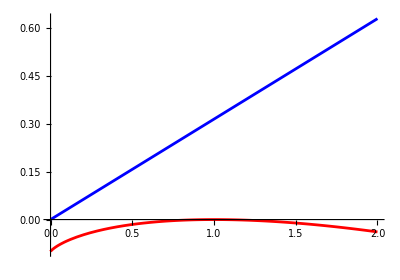

```mathematica
Show[Plot[Re[OSF0[s,M0,α0]],{s,0,2},PlotStyle->Red],Plot[Im[OSF0[s,M0,α0]],{s,0,2},PlotStyle->Blue],PlotRange->Full,AspectRatio->0.7,MaxRecursion->10]
```

```mathematica
Peak[a_?NumericQ]:=Sqrt[s/.Last[NMaximize[Abs[s-1+OSF0[s,1,a]]^-2,s]]];
```

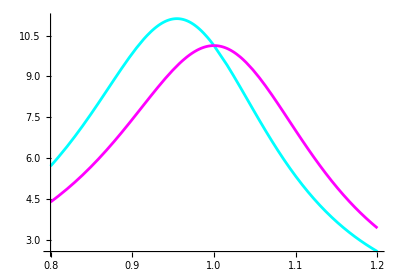

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+OSF0[s,1,α0]]^-2},{s,0.64,1.44},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[s-1+ⅈ 2π α0]^-2},{s,0.64,1.44},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

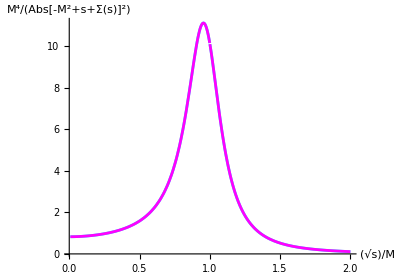

```mathematica
Show[ParametricPlot[{Sqrt[s]/M0,Abs[s-M0^2+OSF0[s,M0,α0]]^-2},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s]/100,Abs[s-100^2+OSF0[s,100,α0]]^-2 100^4},{s,0,4×100^2},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/M,Abs[s-M^2+Σ[s]]^-2 M^4}]
```

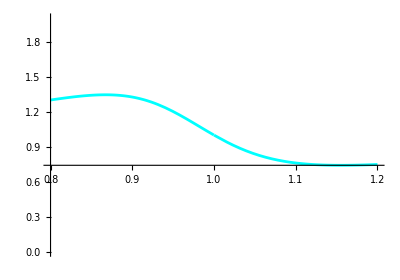

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+OSF0[s,1,α0]]^-2/Abs[s-1+ⅈ 2π α0]^-2},{s,0.64,1.44},PlotStyle->Cyan],AspectRatio->0.7,PlotRange->{0,2},MaxRecursion->10]
```

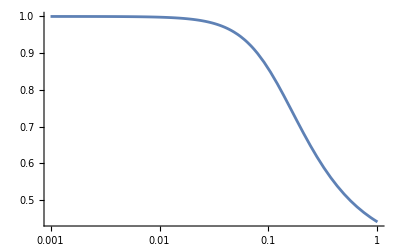

```mathematica
LogLinearPlot[Peak[a],{a,0.001,1}]
```

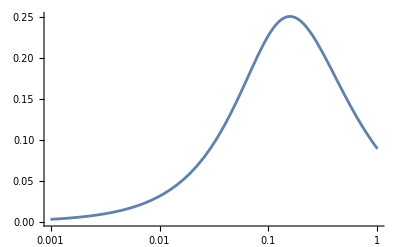

```mathematica
LogLinearPlot[(1-Peak[a])/(2π a),{a,0.001,1}]
```

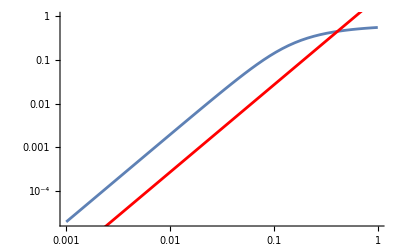

```mathematica
Show[LogLogPlot[1-Peak[a],{a,0.001,1}],Plot[2x+1,{x,-8,0},PlotStyle->Red]]
```

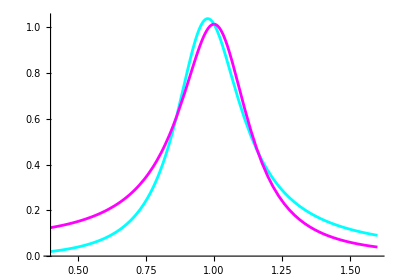

```mathematica
SpectralF[s_,α_]:=-1/π Im[1/(s-1+OSF0[s,1,α])];
Show[ParametricPlot[{Sqrt[s],SpectralF[s,α0]},{s,0.16,2.56},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],SpectralC[s,ΓF0]},{s,0.16,2.56},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

```mathematica
F1[s_]:=s/18 (5+3Log[-1/s]+6π×ⅈ);
FPrime1[s_]:=1/9+1/6 Log[-1/s]+1/3 π×ⅈ;
OSF1[s_,M_,α_]:=12α(F1[s]-Re[F1[M^2]]-(s-M^2)Re[FPrime1[M^2]]);
PMassSqF[M_?NumericQ,α_?NumericQ]:=s/.FindRoot[s-M^2+OSF1[s,M,α],{s,M}]
```

```mathematica
PMassSqF[M0,α0]
```

0.907286-0.282726 ⅈ

```mathematica
M1=1-0.3ⅈ
```

1.-0.3 ⅈ

```mathematica
COSF0[s_,M_,α_]:=12α(F0[s]-F1[M^2]-(s-M^2)FPrime1[M^2]);
```

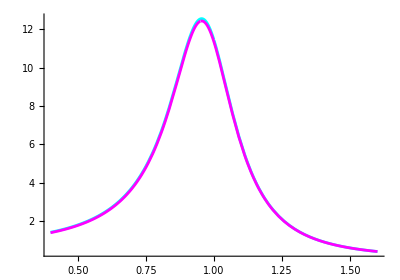

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[1+12α0(FPrime1[PMassSqF[M0,α0]]-Re[FPrime0[M0^2]])]^2 Abs[s-M0^2+OSF0[s,M0,α0]]^-2},{s,0.16,2.56},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[s-PMassSqF[M0,α0]+COSF0[s,Sqrt[PMassSqF[M0,α0]],α0]]^-2},{s,0.16,2.56},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

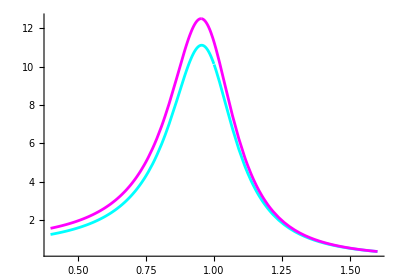

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+OSF0[s,1,α0]]^-2},{s,0.16,2.56},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[s-PMassSqF[M0,α0]]^-2},{s,0.16,2.56},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

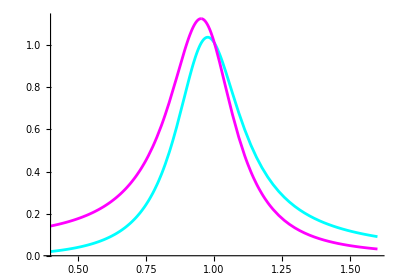

```mathematica
Show[ParametricPlot[{Sqrt[s],SpectralF[s,α0]},{s,0.16,2.56},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],-1/π Im[1/(s-PMassSqF[M0,α0])]},{s,0.16,2.56},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

```mathematica
S0[s_]:=2+Log[-1/s];
SPrime0[s_]:=-1/s;
OSS0[s_,M_,α_]:=α M^2(S0[s]-Re[S0[M^2]]-(s-M^2)Re[SPrime0[M^2]]);
```

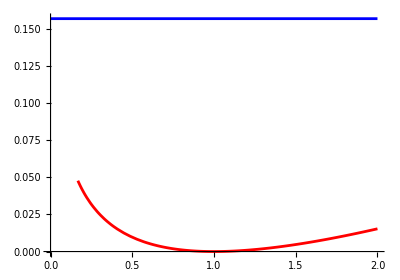

```mathematica
Show[Plot[Re[OSS0[s,M0,α0]],{s,0,2},PlotStyle->Red],Plot[Im[OSS0[s,M0,α0]],{s,0,2},PlotStyle->Blue],PlotRange->Full,AspectRatio->0.7,MaxRecursion->10]
```

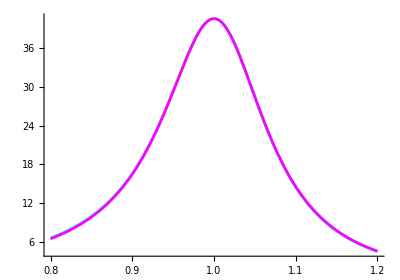

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+OSS0[s,1,α0]]^-2},{s,0.64,1.44},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],Abs[s-1+ⅈ π α0]^-2},{s,0.64,1.44},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

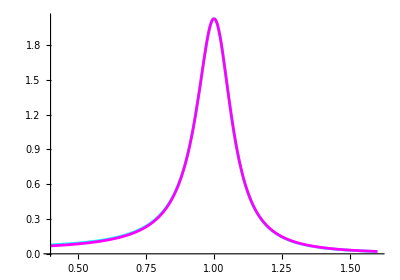

```mathematica
SpectralS[s_,α_]:=-1/π Im[1/(s-1+OSS0[s,1,α])];
Show[ParametricPlot[{Sqrt[s],SpectralS[s,α0]},{s,0.16,2.56},PlotStyle->Cyan],ParametricPlot[{Sqrt[s],SpectralC[s,ΓS0]},{s,0.16,2.56},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10]
```

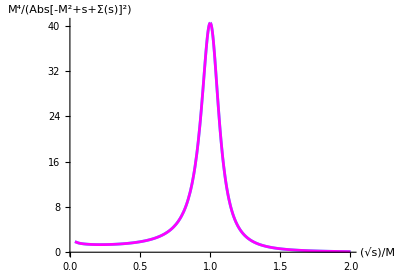

```mathematica
Show[ParametricPlot[{Sqrt[s]/M0,Abs[s-M0^2+OSS0[s,M0,α0]]^-2},{s,0,4},PlotStyle->Cyan],ParametricPlot[{Sqrt[s]/100,Abs[s-100^2+OSS0[s,100,α0]]^-2 100^4},{s,0,4×100^2},PlotStyle->Magenta],AspectRatio->0.7,PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/M,Abs[s-M^2+Σ[s]]^-2 M^4}]
```

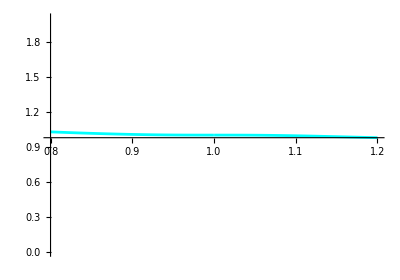

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+OSS0[s,1,0.1]]^-2/Abs[s-1+ⅈ π 0.1]^-2},{s,0.64,1.44},PlotStyle->Cyan],AspectRatio->0.7,PlotRange->{0,2},MaxRecursion->10]
```

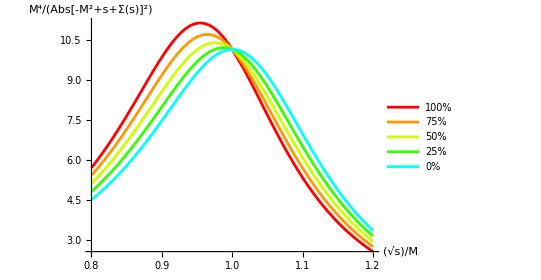

```mathematica
ParametricPlot[{{Sqrt[s],Abs[s-1+OSF0[s,1,α0]]^-2},{Sqrt[s],Abs[s-1+OSF0[s,1,3/4 α0]+OSS0[s,1,1/2 α0]]^-2},{Sqrt[s],Abs[s-1+OSF0[s,1,1/2 α0]+OSS0[s,1,α0]]^-2},{Sqrt[s],Abs[s-1+OSF0[s,1,1/4 α0]+OSS0[s,1,3/2 α0]]^-2},{Sqrt[s],Abs[s-1+OSS0[s,1,2α0]]^-2}},{s,0.64,1.44},PlotRange->Full,AspectRatio->0.7,PlotStyle->{Hue[1],Hue[1.1],Hue[1.2],Hue[1.3],Hue[1.5]},PlotLegends->{"100%","75%","50%", "25%", "0%"},AxesLabel->{Sqrt[s]/M,Abs[s-M^2+Σ[s]]^-2 M^4}]
```